# Leads connected to 1 - 10 and 41 to 50

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
T1[t_]:= t*IdentityMatrix[10]
```

```mathematica
T[t_,m_]:=T[t,m]=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=t*IdentityMatrix[m];MAT]
```

```mathematica
Clear[leads]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["/home/shardul/PhD_new/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[0,3,0.01]}]
```

```mathematica
leads[25]
```

{{{0.-0.848854 ⅈ,0.500319+0. ⅈ,0.+0.170564 ⅈ,-0.00148296+0. ⅈ,0.+0.0219777 ⅈ,0.00302035+0. ⅈ,0.+0.0116615 ⅈ,-0.00381066+0. ⅈ,10,0.+0.000321694 ⅈ,-0.0000155762+0. ⅈ,0.+0.000184309 ⅈ,4.2504×10^-6+0. ⅈ,0.+0.000109971 ⅈ,-1.79988×10^-6+0. ⅈ,0.+0.0000334653 ⅈ},23,{1}},300}
 |  |  |  |

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[m][[Round[ω*100+001]]](*Module[{J=Inverse[β[ω,0.0001,1,0,m]],A:=Inverse[β[ω,0.0001,1,0,m]],T:=T1[1]},Do[J=Inverse[IdentityMatrix[m]-A.T.J.T].A,50000];J=J]*)
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

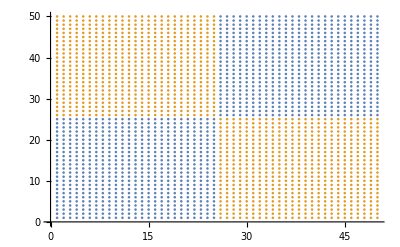

```mathematica
ListPlot[{Join[s[1,25,1,25],s[26,50,26,50]],Join[s[1,25,26,50],s[26,50,1,25]]}]
```

```mathematica
Clear[dist]
```

```mathematica
dist[total_,concentration_]:=dist[total,concentration]=Table[SortBy[Join[RandomSample[Join[s[1,25,1,25],s[26,50,26,50]],concentration],RandomSample[Join[s[1,25,26,50],s[26,50,1,25]],total-concentration]],First],1000]
```

```mathematica
dist[150,75][[1]]
```

{{2,6},{2,7},{2,17},{2,18},{2,43},{3,30},{3,39},{4,11},{4,32},{4,50},{5,5},{5,28},{5,35},{5,37},{6,6},{6,15},{6,28},{6,35},{6,38},{6,48},{6,50},{7,17},{7,27},{8,7},{8,17},{8,22},{8,23},{8,25},{8,27},{8,31},{8,34},{8,35},{9,7},{9,49},{10,4},{10,20},{10,22},{10,36},{12,9},{12,19},{12,33},{13,13},{13,36},{13,44},{13,47},{14,7},{14,17},{14,29},{14,38},{15,22},{15,39},{16,7},{16,26},{19,9},{19,12},{20,19},{20,26},{22,9},{22,24},{22,26},{22,27},{22,33},{23,7},{23,24},{23,27},{23,31},{23,48},{24,29},{24,44},{25,5},{25,32},{26,16},{26,31},{27,1},{27,16},{27,17},{27,34},{28,9},{28,16},{28,19},{28,21},{28,29},{28,49},{28,50},{29,36},{29,39},{30,1},{31,27},{31,33},{31,46},{31,47},{32,3},{32,35},{32,39},{32,45},{33,3},{33,22},{33,35},{33,41},{34,33},{34,36},{35,44},{36,17},{36,19},{36,29},{36,46},{36,49},{37,16},{37,40},{37,44},{38,10},{38,13},{38,14},{38,15},{38,41},{38,46},{39,16},{39,17},{39,48},{40,2},{40,12},{41,12},{41,34},{41,48},{42,28},{42,29},{42,44},{42,47},{43,38},{43,44},{43,48},{44,10},{44,23},{44,25},{44,30},{45,3},{45,10},{46,10},{47,5},{47,8},{47,11},{48,29},{49,8},{49,44},{50,12},{50,22},{50,25},{50,28},{50,29},{50,32}}

```mathematica
TLD[t_]:=Module[{sizeoflead=10},Module[{mat=RandomInteger[0,{50,50}]},ReplacePart[mat,Table[{a,a},{a,1,10}]->t]]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ,50]]
```

```mathematica
Clear[SLLEAD]
```

```mathematica
SLLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
SRLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;10,1;;10]]=LEFT[ω,m];MAT]
```

```mathematica
device1[ω_]:=Module[{sizeoflead=10},Inverse[IdentityMatrix[50]-g[ω,0.0001,1,0].T[1,sizeoflead].SLLEAD[ω,sizeoflead].T[1,sizeoflead]].g[ω,0.0001,1,0]]
```

```mathematica
device1[1][[1,1]]
```

0.376543-0.675031 ⅈ

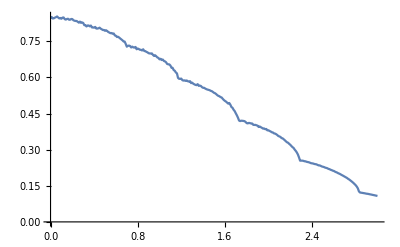

```mathematica
ListLinePlot[Table[{ω,-Im[device1[ω][[1,1]]]},{ω,Range[0,3,0.01]}]]
```

```mathematica
Clear[CA]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,total_,concentration_,number_]:= Module[{sizeoflead=10,abc=dist[total,concentration][[number]]},
recurs=Module[{J1= device1[ω]},
Do[
J1=Inverse[IdentityMatrix[50]-Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]].T[1,50].J1.T[1,50]].Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]],{unitcell,50}];J1=J1];ir=Inverse[IdentityMatrix[50]-SRLEAD[ω,sizeoflead].TLD[1].recurs.TLD[1]].SRLEAD[ω,sizeoflead];il=Inverse[IdentityMatrix[50]-recurs.TLD[1].SRLEAD[ω,sizeoflead].TLD[1]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TLD[1].recurs;
(*Gnonlocallr=recurs.ConjugateTranspose[TLD[1]].ir;*)
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TLD[1].grr1.TLD[1]-TLD[1].GNON1.TLD[1].GNON1]];TRA]
```

```mathematica
Monitor[Table[ParallelTable[CA[1.01,0.0001,1,0,0.5,250,y,n],{n,1000}]//Mean,{y,25,150,25}],y]
```

{2.18459,2.1993,2.19769,2.20677,2.24545,2.24276}

```mathematica
Monitor[Table[Export["/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_half_device_reading_1/ϵ1_150_diag_25_"<>ToString[conc]<>"_.dat",Monitor[Table[{ω,Mean[ParallelTable[CA[ω,0.0001,1,0,1,150,conc,n],{n,1000}]]},{ω,Range[0,3,0.01]}],ω]],{conc,30,120,10}],conc]
```

{/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_half_device_reading_1/ϵ1_150_diag_25_30_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_half_device_reading_1/ϵ1_150_diag_25_40_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_half_device_reading_1/ϵ1_150_diag_25_50_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_half_device_reading_1/ϵ1_150_diag_25_60_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_half_device_reading_1/ϵ1_150_diag_25_70_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_half_device_reading_1/ϵ1_150_diag_25_80_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_half_device_reading_1/ϵ1_150_diag_25_90_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_half_device_reading_1/ϵ1_150_diag_25_100_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_half_device_reading_1/ϵ1_150_diag_25_110_.dat,/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_half_device_reading_1/ϵ1_150_diag_25_120_.dat}

```mathematica
transmission=Table[{x,Import["/home/shardulmukim//PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/diagonal_half_device_reading_1/ϵ1_150_diag_25_"<>ToString[x]<>"_.dat"]},{x,30,120,10}]
```

{{30,{{0.,2.07565},{0.01,1.91337},{0.02,1.74316},{0.03,1.71242},{0.04,1.70406},{0.05,1.7256},{0.06,2.07809},{0.07,3.06608},{0.08,6.98842},284,{2.93,0.957282},{2.94,0.944561},{2.95,0.945246},{2.96,0.983039},{2.97,0.978391},{2.98,0.981264},{2.99,0.998199},{3.,0.971935}}},8,{120,{1}}}
 |  |  |  |

```mathematica
a=(*Manipulate[*)Show[ListLinePlot[Table[{ω,CA[ω,0.0001,1,0,1,50,25,1]},{ω,Range[0,3,0.01]}],Frame->True,PlotRange->{{0,3},{0,25}},(*Epilog->{Dynamic[If[True,Locator[Dynamic[pt],%20,ImageSize->250],{}]]},*)PlotStyle->Red,Frame->True,FrameLabel->{{HoldForm[χ],None},{HoldForm[N],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]},FrameTicks->{{Range[5,20,5],None},{Automatic,None}}],ListLinePlot[Table[{ω,CA[ω,0.0001,1,0,1,50,10,1]},{ω,Range[0,3,0.01]}],Frame->True,PlotStyle->{Brown},PlotRange->{{0,3},{0,25}}],FrameLabel->{{HoldForm[Τ],None},{HoldForm[Ε],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]},ImageSize->500](*,{pt,Scaled[{0.5,0.5}],None}]*)
```

```mathematica
input=Table[ParallelTable[{ω,CA[ω,0.0001,1,0,1,150,80,n]},{ω,Range[0,3,0.01]}],{n,50}]
```

{{{0.,0.843635},{0.01,0.996351},{0.02,4.56679},{0.03,0.230996},294,{2.98,1.30768},{2.99,0.488243},{3.,0.105373}},48,{1}}
 |  |  |  |

```mathematica
misfit[x_,y_,n_]:=Module[{m5=input[[n]]},
ρ1=Table[{transmission[[con,1]],1*Module[{B1=Transpose[{m5[[1;;301]][[;;,1]],(m5[[1;;301,2]]-transmission[[con,2]][[1;;301,;;]][[;;,2]])^2}]},NIntegrate[Interpolation[B1][ω],{ω,y,x}]/((x-y))(*+NIntegrate[Interpolation[B1][ω],{ω,-3,-0.5}]/((2.5)*100)*)]},{con,10}];lista=ρ1(*,ρ2,ρ3,ρ4*)(*,ρ5,ρ6*);
{lista,lista[[Position[lista,Min[lista]][[1,1]]]]}]
```

```mathematica
misfit[3,0.2,1]
```

{{{30,0.586151},{40,0.617382},{50,0.664558},{60,0.768675},{70,0.835595},{80,0.935877},{90,1.04048},{100,1.11789},{110,1.21236},{120,1.27341}},{30,0.586151}}

```mathematica
Table[misfit[3,0.4,n][[2]][[1]],{n,50}]
```

{100,100,80,80,120,110,90,90,90,50,80,60,100,90,80,80,100,80,70,60,80,60,50,80,90,90,110,60,60,80,80,70,70,70,120,100,70,80,80,90,70,70,70,70,110,80,70,70,70,90}

```mathematica
d1[x_,n_]:=d1[x,n]=Mean[Table[misfit[x,y,n][[2]][[1]],{y,0.4,x-0.1,0.02}]]
```

```mathematica
Table[Table[ParallelTable[misfit[x,y,n][[2]][[1]],{y,0.0,x-0.1,0.05}],{x,Range[0.75,2,0.05]}],{n,50}]
```

{{{70,70,60,70,70,70,70,70,70,70,70,70,70,90},24,{80,80,70,90,90,90,90,90,90,90,90,100,100,100,100,110,110,110,110,100,80,60,60,80,80,80,90,100,90,80,80,80,60,60,60,80,90,90,80}},48,{1}}
 |  |  |  |

```mathematica
%86[[1]]
```

30

```mathematica
Abs[N[Table[Mean[Flatten[%121[[n]]]],{n,50}]]]
```

{88.5486,88.2874,72.2206,78.1567,106.154,103.396,84.775,91.8578,88.6067,70.7837,68.897,63.6284,88.0552,87.8955,83.701,81.8868,100.029,74.7315,64.7315,58.1277,82.7141,63.4253,48.1422,87.1553,91.2772,88.7518,98.0116,71.582,62.9318,85.4572,77.5472,76.1538,82.9173,78.6212,116.807,90.7837,79.4775,71.5675,83.6865,91.5965,75.254,67.9971,67.3004,81.045,91.3643,82.5254,68.0552,63.5704,69.3759,98.1277}

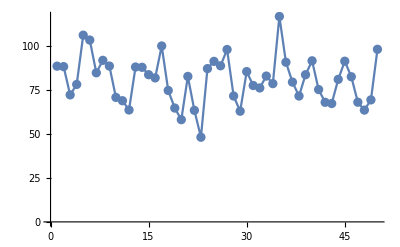

```mathematica
ListLinePlot[%118,Mesh->All]
```

```mathematica
xxx=Monitor[Table[Mean[ParallelTable[d1[x,n],{x,Range[0.75,2,0.05]}]],{n,50}],n]
```

{{804051218477780059968709615/7671623816751318572616468,1.18356},{23256334742399130382804632515/276178457403047468614192848,0.482833},{14428730759046188104010702395/138089228701523734307096424,0.813335},{352110092062127954470472315/3586733213026590501483024,3.49023},{202592900015950867919250985/2465879083955780969769579,0.60305},{1813105462141730429739434215/17261153587690466788387053,0.501985},{69438489525204566278605425/713639424814076146289904,0.651821},{2942247561360627717133976795/39454065343292495516313264,0.32},{10078102553190073265731975/114739699793538624268464,2.63505},{55897480128677593560478045/556811406054531186722163,0.55049},{8904420966638131581858696305/92059485801015822871397616,0.435172},{2965867386951940675235392945/39454065343292495516313264,0.663307},{31828353495824505312708394495/276178457403047468614192848,0.632493},{28051135285433435165365255235/276178457403047468614192848,1.02145},{43258008907297709318413985/444731815463844554934288,0.497624},{75737397059684452090939445/793616256905308817856876,0.77221},{317462810478887706425541935/2969660832290832995851536,0.636917},{882661882818662281059939685/10228831755668424763488624,1.11856},{12027154432893122096995488185/138089228701523734307096424,0.693314},{365905815135404541622111945/3783266539767773542660176,1.27975},{15044312194929066319943376815/138089228701523734307096424,0.968642},{1229476998443062272266543105/17261153587690466788387053,0.623828},{1984554820867792218259475245/19727032671646247758156632,0.658945},{240266833053531598857679165/3287838778607707959692772,0.440995},{1333159192232901058216376465/13151355114430831838771088,0.936228},{187722634214694222213425/1791877253990497953741,1.47941},{21106590711798286691083385/200419780408597582448616,0.504482},{398680915847957572433440115/4061447902985992185502836,0.591787},{1268049792751394488693306655/13151355114430831838771088,0.618364},{489947273935721279461168295/4931758167911561939539158,0.842627},{26936037553855345141163874665/276178457403047468614192848,0.478835},{6472006862274913354116355/68598722653514025984648,0.771974},{13863440941178465450803442815/138089228701523734307096424,0.914326},{25278213000354004212510938905/276178457403047468614192848,0.750422},{3047751250876851758041009685/30686495267005274290465872,0.37809},{9946232363190912729277012105/138089228701523734307096424,0.60148},{175459391764029556228249405/2030723951492996092751418,0.623136},{9318567573930799740310602755/92059485801015822871397616,3.05067},{14457053082643804597716371135/138089228701523734307096424,0.576527},{24441277698343632384768279415/276178457403047468614192848,0.513303},{1205982645733764868959147445/13151355114430831838771088,0.644021},{869476963244073422224641745/9523395082863705814282512,0.664674},{33825522559574086404207395/353169382868347146565464,0.459334},{1142291840329891951900483385/10622248361655671869776648,1.77643},{12131790481158579144952576865/138089228701523734307096424,0.760419},{379920826738492719119678065/3540749453885223956592216,1.20811},{660399538147155515873951255/6575677557215415919385544,1.21033},{891423580434003763232375455/9523395082863705814282512,0.909544},{3019243171476809021027083285/30686495267005274290465872,0.929424},{84435634857890278188553235/1327781045206958983722081,0.599242}}

```mathematica
StandardDeviation[Transpose[xxx][[1]]-100]
```

(√(57328843537563851825206862851628515251942399814083455149/2))/483312300455333070074837484

```mathematica
N[(√(57328843537563851825206862851628515251942399814083455149/2))/483312300455333070074837484]
```

11.0776

```mathematica
N[(√165307054720765063789964571196460036217145652573)/30809734203820556516532]
```

13.1965

```mathematica
Table[misfit[3.,0.15,n][[2]][[1]],{n,100}]
```

{20,15,15,15,25,10,15,30,15,20,15,25,20,15,30,25,20,10,15,25,15,45,5,40,30,15,45,15,15,25,15,20,30,30,25,20,20,15,10,30,35,20,45,25,30,10,30,20,15,20,20,20,35,30,20,15,20,25,25,20,20,35,25,35,30,35,40,25,15,20,35,25,20,30,20,35,15,15,35,35,20,25,25,45,20,15,30,35,35,15,20,40,20,25,25,25,25,40,30,30}

```mathematica
Table[Mean[Abs[Table[misfit[X+0.5,X,n][[2]][[1]],{X,0,2.49,0.02}]-25]]/25,{n,100}]//Mean
```

$Aborted

```mathematica
Mean[%78]
```

2267/6250

```mathematica
N[2267/6250]
```

0.36272

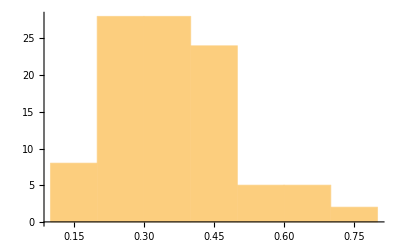

```mathematica
Histogram[%78]
```

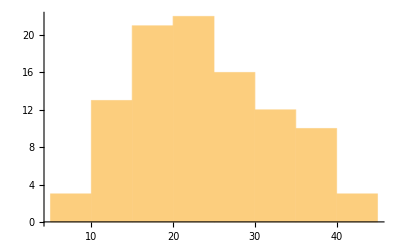

```mathematica
Histogram[%74]
```

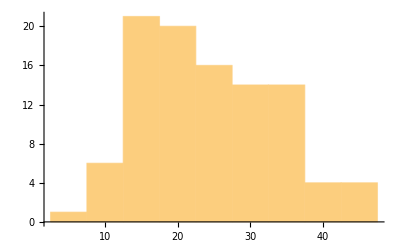

```mathematica
Histogram[%71]
```

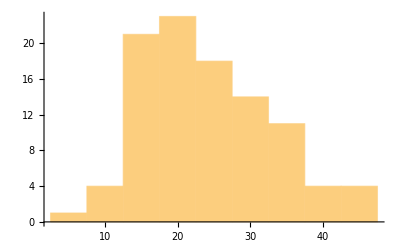

```mathematica
Histogram[%69]
```

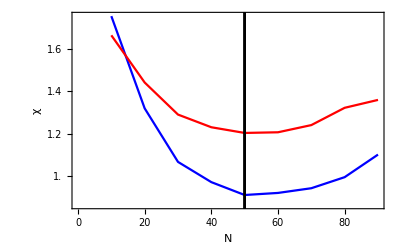

```mathematica
Show[ListLinePlot[misfit[2,0,1][[1]],Frame->True,PlotStyle->Blue,FrameStyle->{Directive[Black,13],Directive[Black,13]},FrameLabel->{{HoldForm[χ],None},{HoldForm[N],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]},FrameTicks->{{Range[0.8,1.6,0.2],None},{Automatic,None}}],ListLinePlot[misfit[2,0,2][[1]],Frame->True,PlotStyle->Red],ListLinePlot[Table[{50,x},{x,{0.5,2,0.00001}}],PlotStyle->Black]]
```

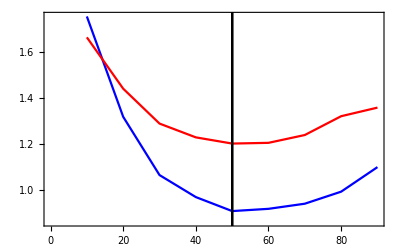

```mathematica
Show[%48,AxesStyle->Black]
```

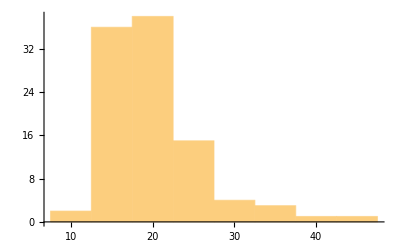

```mathematica
Histogram[%52]
```

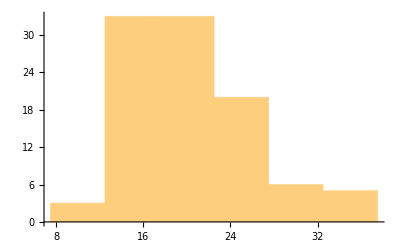

```mathematica
Histogram[%49]
```

```mathematica
Mean[Table[Abs[misfit[3,0.5,n][[2]][[1]]-35]/35,{n,100}]]//N
```

0.17

```mathematica
Table[misfit[3,0.5,n][[2]][[1]],{n,100}]
```

{20,15,20,20,20,20,15,15,20,20,15,15,20,15,15,15,20,20,15,15,15,20,15,15,20,15,15,15,15,15,15,15,20,15,20,15,20,20,15,15,15,20,20,20,15,15,15,15,15,15,15,20,15,20,25,15,15,20,15,25,20,15,20,15,15,20,20,15,15,15,15,20,20,10,20,20,20,15,20,20,15,20,20,20,20,20,20,15,20,20,15,20,20,15,15,15,20,25,15,15}

```mathematica
Abs[Table[Mean[Table[misfit[x+0.25,x,y][[2]][[1]],{x,Range[0,2,0.05]}]],{y,100}]]//N
```

{17.8049,19.878,20.7317,21.7073,25.122,19.5122,18.0488,22.8049,20.,22.0732,27.6829,21.3415,23.6585,17.8049,18.7805,19.6341,16.2195,27.1951,15.2439,27.9268,25.122,21.5854,21.3415,18.7805,28.0488,18.2927,18.0488,15.8537,17.1951,29.878,12.439,18.2927,13.9024,22.3171,18.1707,22.439,21.2195,23.2927,20.9756,25.4878,22.561,29.1463,22.0732,31.8293,14.878,17.9268,18.1707,23.7805,18.0488,23.4146,20.9756,25.122,32.1951,23.9024,27.1951,17.3171,19.3902,16.3415,17.561,26.3415,17.3171,20.,17.439,21.3415,25.,22.3171,27.0732,17.439,16.5854,18.2927,16.3415,19.878,23.2927,16.8293,24.3902,19.5122,17.8049,16.9512,12.561,24.878,14.7561,16.0976,28.7805,29.6341,25.8537,17.8049,21.9512,14.3902,12.9268,27.439,20.122,24.1463,21.7073,19.2683,14.5122,16.5854,21.9512,21.2195,16.2195,23.2927}

```mathematica
Gather[%59]
```

{{17.8049,17.8049,17.8049,17.8049},{19.878,19.878},{20.7317},{21.7073,21.7073},{25.122,25.122,25.122},{19.5122,19.5122},{18.0488,18.0488,18.0488},{22.8049},{20.,20.},{22.0732,22.0732},{27.6829},{21.3415,21.3415,21.3415},{23.6585},{18.7805,18.7805},{19.6341},{16.2195,16.2195},{27.1951,27.1951},{15.2439},{27.9268},{21.5854},{28.0488},{18.2927,18.2927,18.2927},{15.8537},{17.1951},{29.878},{12.439},{13.9024},{22.3171,22.3171},{18.1707,18.1707},{22.439},{21.2195,21.2195},{23.2927,23.2927,23.2927},{20.9756,20.9756},{25.4878},{22.561},{29.1463},{31.8293},{14.878},{17.9268},{23.7805},{23.4146},{32.1951},{23.9024},{17.3171,17.3171},{19.3902},{16.3415,16.3415},{17.561},{26.3415},{17.439,17.439},{25.},{27.0732},{16.5854,16.5854},{16.8293},{24.3902},{16.9512},{12.561},{24.878},{14.7561},{16.0976},{28.7805},{29.6341},{25.8537},{21.9512,21.9512},{14.3902},{12.9268},{27.439},{20.122},{24.1463},{19.2683},{14.5122}}

```mathematica
StandardDeviation[%59]
```

4.43194

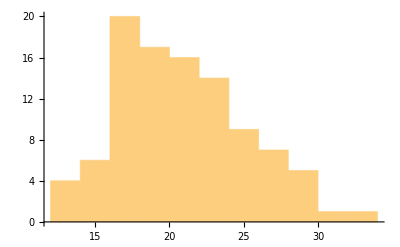

```mathematica
Histogram[%59]
```

```mathematica
Mean[%57]
```

0.180915

```mathematica
Table[Mean[Table[misfit[x+0.25,x,y][[1]],{x,Range[0,2.5,0.05]}]],{y,100}]//N
```

{{{5.,0.00559353},{10.,0.00476808},{15.,0.00451279},{20.,0.00477025},{25.,0.00532946},{30.,0.00619385},{35.,0.00692866},{40.,0.00806695},{45.,0.00922956}},{{5.,0.00732038},{10.,0.00593592},{15.,0.00519216},{20.,0.00495782},{25.,0.00491543},{30.,0.00527422},{35.,0.00591651},{40.,0.00647985},{45.,0.00719245}},{{5.,0.00680329},{10.,0.00563333},{15.,0.00513779},{20.,0.00483637},{25.,0.00508906},{30.,0.00553032},{35.,0.00609963},{40.,0.00699562},{45.,0.00790023}},{{5.,0.00779831},{10.,0.00684206},{15.,0.00636675},{20.,0.0066729},{25.,0.00712802},{30.,0.00779029},{35.,0.00833323},{40.,0.0092651},{45.,0.0102838}},{{5.,0.0101246},{10.,0.00834106},{15.,0.00712741},{20.,0.00657815},{25.,0.00629784},{30.,0.00642024},{35.,0.00662626},{40.,0.00699558},{45.,0.00754155}},{{5.,0.00579287},{10.,0.00496443},{15.,0.0046635},{20.,0.00456241},{25.,0.00491697},{30.,0.0055675},{35.,0.00613261},{40.,0.00721751},{45.,0.00819459}},{{5.,0.00602716},{10.,0.00508366},{15.,0.00463148},{20.,0.00469404},{25.,0.00513492},{30.,0.00579688},{35.,0.00641327},{40.,0.00748475},{45.,0.00846496}},{{5.,0.00765343},{10.,0.00600001},{15.,0.00499621},{20.,0.00457412},{25.,0.00453068},{30.,0.00482144},{35.,0.00495473},{40.,0.00555583},{45.,0.00628544}},{{5.,0.00687424},{10.,0.00572628},{15.,0.00512639},{20.,0.00514282},{25.,0.00530902},{30.,0.00592691},{35.,0.00656867},{40.,0.00737559},{45.,0.00831529}},{{5.,0.0160178},{10.,0.0145779},{15.,0.0138102},{20.,0.0130498},{25.,0.0128341},{30.,0.0130244},{35.,0.0134605},{40.,0.0141058},{45.,0.0149071}},{{5.,0.00768319},{10.,0.00609677},{15.,0.0051647},{20.,0.00491538},{25.,0.0047918},{30.,0.0050856},{35.,0.00540784},{40.,0.0059909},{45.,0.00672813}},{{5.,0.00942591},{10.,0.00785925},{15.,0.00705101},{20.,0.00670535},{25.,0.00676689},{30.,0.00710562},{35.,0.00764588},{40.,0.00809772},{45.,0.00900493}},{{5.,0.0101277},{10.,0.00868597},{15.,0.00753779},{20.,0.0068985},{25.,0.00664786},{30.,0.00664195},{35.,0.00677869},{40.,0.00728114},{45.,0.00774969}},{{5.,0.00900173},{10.,0.00793367},{15.,0.00718552},{20.,0.00683366},{25.,0.00682322},{30.,0.00701736},{35.,0.00762066},{40.,0.00847058},{45.,0.0090039}},{{5.,0.00675535},{10.,0.00549411},{15.,0.00464963},{20.,0.00443408},{25.,0.00468435},{30.,0.00512213},{35.,0.00555118},{40.,0.00640578},{45.,0.00741934}},{{5.,0.0057436},{10.,0.0049371},{15.,0.00478448},{20.,0.00487311},{25.,0.00530741},{30.,0.0060407},{35.,0.00674577},{40.,0.00795147},{45.,0.00896319}},{{5.,0.00855515},{10.,0.00748456},{15.,0.00698386},{20.,0.00692943},{25.,0.00701455},{30.,0.00749149},{35.,0.00820305},{40.,0.00891237},{45.,0.00992555}},{{5.,0.00833145},{10.,0.00676848},{15.,0.0058381},{20.,0.00536411},{25.,0.00530611},{30.,0.00538332},{35.,0.00559117},{40.,0.00621444},{45.,0.0069007}},{{5.,0.00651917},{10.,0.00547154},{15.,0.00495664},{20.,0.00506696},{25.,0.00555437},{30.,0.00629922},{35.,0.00711392},{40.,0.00803213},{45.,0.00927318}},{{5.,0.0122218},{10.,0.010583},{15.,0.00989853},{20.,0.00948692},{25.,0.00941468},{30.,0.00953576},{35.,0.00981267},{40.,0.0103376},{45.,0.0108924}},{{5.,0.0114473},{10.,0.00939897},{15.,0.00802348},{20.,0.00730312},{25.,0.00685967},{30.,0.00690403},{35.,0.00696161},{40.,0.00740684},{45.,0.00791731}},{{5.,0.00660445},{10.,0.00530091},{15.,0.0046548},{20.,0.00462601},{25.,0.00488971},{30.,0.00539672},{35.,0.00580517},{40.,0.00656526},{45.,0.00750047}},{{5.,0.0250196},{10.,0.0236389},{15.,0.0225816},{20.,0.0221488},{25.,0.0220952},{30.,0.0222862},{35.,0.0224948},{40.,0.0234194},{45.,0.024204}},{{5.,0.00807596},{10.,0.00686846},{15.,0.00605808},{20.,0.00568158},{25.,0.0057605},{30.,0.00610039},{35.,0.00678997},{40.,0.00748532},{45.,0.00839528}},{{5.,0.0210518},{10.,0.0191523},{15.,0.0181281},{20.,0.0172025},{25.,0.0168475},{30.,0.0165293},{35.,0.0164389},{40.,0.016827},{45.,0.0172097}},{{5.,0.00668757},{10.,0.00526071},{15.,0.00446756},{20.,0.00430124},{25.,0.00444437},{30.,0.00499236},{35.,0.005393},{40.,0.00623225},{45.,0.00724758}},{{5.,0.00686626},{10.,0.00544646},{15.,0.0048434},{20.,0.00474161},{25.,0.00494881},{30.,0.00549321},{35.,0.00608232},{40.,0.00689078},{45.,0.00791586}},{{5.,0.00553806},{10.,0.00470577},{15.,0.00433365},{20.,0.00428242},{25.,0.00458728},{30.,0.00517835},{35.,0.00580468},{40.,0.00689498},{45.,0.00772906}},{{5.,0.00650782},{10.,0.00517555},{15.,0.00446001},{20.,0.00428059},{25.,0.00438755},{30.,0.00479574},{35.,0.00533949},{40.,0.00604864},{45.,0.00696581}},{{5.,0.00601244},{10.,0.00476311},{15.,0.0042033},{20.,0.0040769},{25.,0.00423074},{30.,0.00474482},{35.,0.00536873},{40.,0.00607958},{45.,0.00692299}},{{5.,0.00619521},{10.,0.00531302},{15.,0.00501234},{20.,0.00502777},{25.,0.00563501},{30.,0.00633857},{35.,0.00689553},{40.,0.00824303},{45.,0.00921849}},{{5.,0.0192787},{10.,0.0181012},{15.,0.0171134},{20.,0.0162821},{25.,0.015967},{30.,0.0157417},{35.,0.0157669},{40.,0.0163033},{45.,0.0164801}},{{5.,0.00532025},{10.,0.00453523},{15.,0.00439501},{20.,0.00467495},{25.,0.00526357},{30.,0.00608363},{35.,0.00699103},{40.,0.00808997},{45.,0.00926659}},{{5.,0.00850758},{10.,0.00697538},{15.,0.00599478},{20.,0.00537647},{25.,0.00531203},{30.,0.00542313},{35.,0.00573647},{40.,0.00648493},{45.,0.00700408}},{{5.,0.00630954},{10.,0.00513294},{15.,0.00453057},{20.,0.00449604},{25.,0.00484453},{30.,0.0054605},{35.,0.00589871},{40.,0.00695326},{45.,0.00787878}},{{5.,0.00647377},{10.,0.00497545},{15.,0.00424481},{20.,0.00410989},{25.,0.0042967},{30.,0.00479955},{35.,0.0051411},{40.,0.0059648},{45.,0.00684173}},{{5.,0.00748712},{10.,0.00626296},{15.,0.00550254},{20.,0.00541225},{25.,0.00549038},{30.,0.00598731},{35.,0.00679168},{40.,0.00738445},{45.,0.00828386}},{{5.,0.00957493},{10.,0.00847269},{15.,0.00789172},{20.,0.00772214},{25.,0.00792128},{30.,0.00835857},{35.,0.00885067},{40.,0.00962507},{45.,0.0104489}},{{5.,0.00630991},{10.,0.005205},{15.,0.00471199},{20.,0.00465288},{25.,0.00502023},{30.,0.0055666},{35.,0.00614768},{40.,0.00700138},{45.,0.00808261}},{{5.,0.0109257},{10.,0.00907731},{15.,0.00774419},{20.,0.0071632},{25.,0.00678789},{30.,0.00677407},{35.,0.00680006},{40.,0.00711432},{45.,0.00749671}},{{5.,0.00871015},{10.,0.00727359},{15.,0.00660233},{20.,0.00632837},{25.,0.00632848},{30.,0.00680695},{35.,0.00711035},{40.,0.00781492},{45.,0.00861593}},{{5.,0.00789279},{10.,0.00624761},{15.,0.00528217},{20.,0.00488781},{25.,0.00482913},{30.,0.00515464},{35.,0.00538783},{40.,0.00599071},{45.,0.00671551}},{{5.,0.00750056},{10.,0.00635203},{15.,0.00556413},{20.,0.00524075},{25.,0.00534374},{30.,0.00572134},{35.,0.00622569},{40.,0.00721385},{45.,0.00796629}},{{5.,0.0297676},{10.,0.0281886},{15.,0.0267255},{20.,0.0259974},{25.,0.0250744},{30.,0.0248225},{35.,0.0262032},{40.,0.0256135},{45.,0.0261008}},{{5.,0.00550761},{10.,0.0045114},{15.,0.00417475},{20.,0.00429003},{25.,0.00475565},{30.,0.00551073},{35.,0.0061945},{40.,0.00719835},{45.,0.00827352}},{{5.,0.00483961},{10.,0.00405654},{15.,0.00373877},{20.,0.00382684},{25.,0.00434745},{30.,0.00517845},{35.,0.00604958},{40.,0.00725449},{45.,0.00833763}},{{5.,0.00591678},{10.,0.00502453},{15.,0.00488585},{20.,0.00520844},{25.,0.00572299},{30.,0.00649827},{35.,0.00719344},{40.,0.00831032},{45.,0.009428}},{{5.,0.00862723},{10.,0.00715075},{15.,0.00629003},{20.,0.00587794},{25.,0.00591555},{30.,0.00616394},{35.,0.00657317},{40.,0.00724114},{45.,0.00809034}},{{5.,0.0072896},{10.,0.00588881},{15.,0.00494045},{20.,0.00460877},{25.,0.00469278},{30.,0.00512599},{35.,0.00563407},{40.,0.00645423},{45.,0.0073497}},{{5.,0.00829117},{10.,0.00727176},{15.,0.00671392},{20.,0.00636106},{25.,0.0065339},{30.,0.0068997},{35.,0.00750327},{40.,0.00841093},{45.,0.00929814}},{{5.,0.00871154},{10.,0.00779589},{15.,0.00734242},{20.,0.00736904},{25.,0.00758311},{30.,0.00811983},{35.,0.00928363},{40.,0.00995052},{45.,0.0109358}},{{5.,0.006716},{10.,0.00580518},{15.,0.00550609},{20.,0.00550794},{25.,0.00587647},{30.,0.00653605},{35.,0.00706047},{40.,0.00786275},{45.,0.00876771}},{{5.,0.0122975},{10.,0.00999835},{15.,0.00843772},{20.,0.00745591},{25.,0.00685603},{30.,0.00664115},{35.,0.00642525},{40.,0.00671115},{45.,0.0068693}},{{5.,0.00659288},{10.,0.00560024},{15.,0.00503},{20.,0.00477202},{25.,0.00487043},{30.,0.00519512},{35.,0.00565569},{40.,0.00643917},{45.,0.00709168}},{{5.,0.00816498},{10.,0.00660663},{15.,0.00565552},{20.,0.00505352},{25.,0.00486404},{30.,0.00505662},{35.,0.00519983},{40.,0.00584679},{45.,0.00636147}},{{5.,0.00711564},{10.,0.00615006},{15.,0.00583147},{20.,0.00597369},{25.,0.00641925},{30.,0.00723273},{35.,0.00799448},{40.,0.00897467},{45.,0.010032}},{{5.,0.00716417},{10.,0.00600016},{15.,0.005368},{20.,0.00511396},{25.,0.00534641},{30.,0.00582702},{35.,0.00620607},{40.,0.00735732},{45.,0.00825081}},{{5.,0.00532489},{10.,0.0043556},{15.,0.00388911},{20.,0.00380392},{25.,0.0040218},{30.,0.00455062},{35.,0.00514981},{40.,0.00612793},{45.,0.0069088}},{{5.,0.00756953},{10.,0.00658597},{15.,0.0064307},{20.,0.00638055},{25.,0.00676187},{30.,0.00759858},{35.,0.00827078},{40.,0.00927679},{45.,0.0102957}},{{5.,0.00811817},{10.,0.00654936},{15.,0.00564467},{20.,0.00537113},{25.,0.00535959},{30.,0.00578693},{35.,0.00650488},{40.,0.00712732},{45.,0.008175}},{{5.,0.00718165},{10.,0.00625169},{15.,0.00567156},{20.,0.0056268},{25.,0.00580856},{30.,0.00637965},{35.,0.00680727},{40.,0.00784424},{45.,0.00847689}},{{5.,0.0137578},{10.,0.0123888},{15.,0.0117846},{20.,0.0115972},{25.,0.0115452},{30.,0.0117045},{35.,0.0120344},{40.,0.0122548},{45.,0.0130237}},{{5.,0.00552118},{10.,0.00433588},{15.,0.00379505},{20.,0.00385042},{25.,0.00414533},{30.,0.00478005},{35.,0.00543615},{40.,0.00630341},{45.,0.0073175}},{{5.,0.0109898},{10.,0.0101826},{15.,0.00968383},{20.,0.00995353},{25.,0.0102001},{30.,0.0108246},{35.,0.0114757},{40.,0.0121965},{45.,0.0131428}},{{5.,0.0139342},{10.,0.0127643},{15.,0.0118777},{20.,0.0115056},{25.,0.0113457},{30.,0.01167},{35.,0.0127716},{40.,0.0129653},{45.,0.0137758}},{{5.,0.00728163},{10.,0.00605476},{15.,0.00548856},{20.,0.00537598},{25.,0.00542882},{30.,0.00591614},{35.,0.00669076},{40.,0.00725724},{45.,0.00819981}},{{5.,0.00959515},{10.,0.00793474},{15.,0.00672812},{20.,0.00619689},{25.,0.00590567},{30.,0.0059241},{35.,0.00602144},{40.,0.00646498},{45.,0.00692287}},{{5.,0.00909064},{10.,0.00795984},{15.,0.00714225},{20.,0.00705063},{25.,0.00721755},{30.,0.00769945},{35.,0.00808397},{40.,0.00880944},{45.,0.00958389}},{{5.,0.00560286},{10.,0.0047795},{15.,0.00461248},{20.,0.0048557},{25.,0.00540119},{30.,0.00623751},{35.,0.00699891},{40.,0.00809791},{45.,0.00932274}},{{5.,0.00744604},{10.,0.00628677},{15.,0.00574774},{20.,0.00567475},{25.,0.00587659},{30.,0.00648493},{35.,0.00713063},{40.,0.00789837},{45.,0.00883393}},{{5.,0.0057872},{10.,0.00496431},{15.,0.00461572},{20.,0.00485909},{25.,0.00551648},{30.,0.00633607},{35.,0.00706624},{40.,0.00811868},{45.,0.00937538}},{{5.,0.0103649},{10.,0.00928676},{15.,0.00864838},{20.,0.00863508},{25.,0.00873458},{30.,0.00927835},{35.,0.00977854},{40.,0.0103744},{45.,0.0111664}},{{5.,0.00593182},{10.,0.00489644},{15.,0.00426412},{20.,0.00438632},{25.,0.0047802},{30.,0.00542657},{35.,0.00601822},{40.,0.0069243},{45.,0.00795409}},{{5.,0.0126152},{10.,0.0112858},{15.,0.0107353},{20.,0.0105826},{25.,0.0104941},{30.,0.0109157},{35.,0.0114858},{40.,0.0123397},{45.,0.0129616}},{{5.,0.0100528},{10.,0.00892813},{15.,0.00839385},{20.,0.007897},{25.,0.00797065},{30.,0.00829427},{35.,0.00873182},{40.,0.00958986},{45.,0.0103735}},{{5.,0.00777736},{10.,0.00618629},{15.,0.0052797},{20.,0.00496054},{25.,0.0048516},{30.,0.00511734},{35.,0.00528133},{40.,0.00594762},{45.,0.00657869}},{{5.,0.00587919},{10.,0.00497471},{15.,0.0045738},{20.,0.00474559},{25.,0.0053086},{30.,0.00614196},{35.,0.00684188},{40.,0.00786612},{45.,0.00910132}},{{5.,0.00543931},{10.,0.00458886},{15.,0.00424158},{20.,0.00457926},{25.,0.00520348},{30.,0.0060955},{35.,0.00680337},{40.,0.00800634},{45.,0.00916296}},{{5.,0.00701961},{10.,0.00585585},{15.,0.00538839},{20.,0.00526741},{25.,0.00579291},{30.,0.006477},{35.,0.0069773},{40.,0.0082502},{45.,0.00928937}},{{5.,0.0105143},{10.,0.00908523},{15.,0.0084445},{20.,0.00816754},{25.,0.00812579},{30.,0.00821782},{35.,0.00851636},{40.,0.0089006},{45.,0.00969448}},{{5.,0.0049336},{10.,0.0043833},{15.,0.00430278},{20.,0.00471278},{25.,0.00541032},{30.,0.00640894},{35.,0.00730128},{40.,0.00853131},{45.,0.00980543}},{{5.,0.0198903},{10.,0.0191294},{15.,0.0185296},{20.,0.0188475},{25.,0.0189112},{30.,0.0195576},{35.,0.0202312},{40.,0.0208295},{45.,0.0217278}},{{5.,0.00658942},{10.,0.00528291},{15.,0.00459692},{20.,0.0045492},{25.,0.00481952},{30.,0.00535652},{35.,0.0058766},{40.,0.00658355},{45.,0.00762889}},{{5.,0.0117606},{10.,0.00982634},{15.,0.00854381},{20.,0.00800814},{25.,0.00754989},{30.,0.00750211},{35.,0.00776996},{40.,0.00801319},{45.,0.00852577}},{{5.,0.00687142},{10.,0.00549468},{15.,0.00483958},{20.,0.0046238},{25.,0.00483961},{30.,0.00529091},{35.,0.00564801},{40.,0.00654401},{45.,0.00738015}},{{5.,0.0166342},{10.,0.015626},{15.,0.0149088},{20.,0.014755},{25.,0.0145959},{30.,0.0149947},{35.,0.0164947},{40.,0.0165934},{45.,0.0175148}},{{5.,0.00611252},{10.,0.00510697},{15.,0.00475249},{20.,0.00478496},{25.,0.00503645},{30.,0.00566182},{35.,0.00659406},{40.,0.00744046},{45.,0.00844783}},{{5.,0.00550128},{10.,0.0048557},{15.,0.00481104},{20.,0.00529719},{25.,0.00593928},{30.,0.00700716},{35.,0.00795058},{40.,0.00897356},{45.,0.0102273}},{{5.,0.00605647},{10.,0.00513792},{15.,0.00487269},{20.,0.00512407},{25.,0.00567195},{30.,0.00660391},{35.,0.00752851},{40.,0.00861174},{45.,0.00976167}},{{5.,0.00987356},{10.,0.00815637},{15.,0.00707958},{20.,0.00659199},{25.,0.0064184},{30.,0.00638745},{35.,0.00643577},{40.,0.00678724},{45.,0.00728119}},{{5.,0.00679563},{10.,0.00584589},{15.,0.00528027},{20.,0.00530739},{25.,0.00559622},{30.,0.00625465},{35.,0.00693312},{40.,0.00783861},{45.,0.00888522}},{{5.,0.0108794},{10.,0.00945714},{15.,0.00863742},{20.,0.00854964},{25.,0.00846824},{30.,0.00863668},{35.,0.00896413},{40.,0.00947761},{45.,0.0100558}},{{5.,0.0107571},{10.,0.00923325},{15.,0.00837409},{20.,0.00826196},{25.,0.00850388},{30.,0.00898812},{35.,0.00947395},{40.,0.0103661},{45.,0.0113956}},{{5.,0.00611702},{10.,0.00493302},{15.,0.00425384},{20.,0.00420401},{25.,0.00434531},{30.,0.00488251},{35.,0.00548633},{40.,0.0062004},{45.,0.00716641}},{{5.,0.00582363},{10.,0.00460288},{15.,0.00393562},{20.,0.00388939},{25.,0.00413484},{30.,0.00469001},{35.,0.005275},{40.,0.00631817},{45.,0.00735725}},{{5.,0.00692313},{10.,0.00652451},{15.,0.00650177},{20.,0.00660791},{25.,0.00709062},{30.,0.0077617},{35.,0.00856769},{40.,0.00976782},{45.,0.01068}},{{5.,0.00855112},{10.,0.00763024},{15.,0.00706469},{20.,0.00690399},{25.,0.00714976},{30.,0.00766125},{35.,0.00822591},{40.,0.00914527},{45.,0.00990481}},{{5.,0.00884288},{10.,0.00750045},{15.,0.00641183},{20.,0.00600729},{25.,0.00581585},{30.,0.00609802},{35.,0.00687848},{40.,0.00738982},{45.,0.00806624}},{{5.,0.00867978},{10.,0.00793483},{15.,0.00761314},{20.,0.00792303},{25.,0.00839984},{30.,0.00919452},{35.,0.00996658},{40.,0.0106883},{45.,0.0119146}},{{5.,0.00979028},{10.,0.00787713},{15.,0.00653607},{20.,0.00577126},{25.,0.00540729},{30.,0.0052563},{35.,0.00522158},{40.,0.00573199},{45.,0.00616831}}}

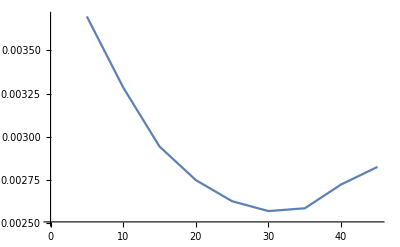

```mathematica
ListLinePlot[%38[[5]]]
```

```mathematica
Mean[%31]
```

39

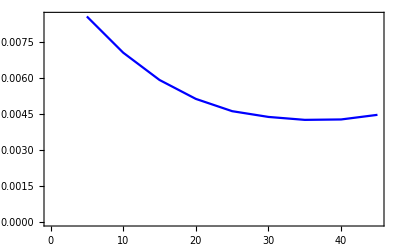

```mathematica
ListLinePlot[misfit[3,0.2,2][[1]],PlotStyle->Blue,Frame->True]
```

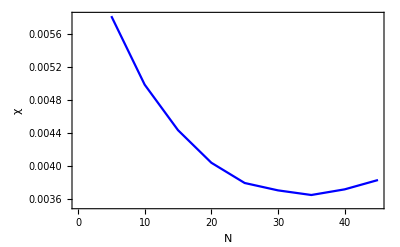

```mathematica
Show[%40,FrameLabel->{{HoldForm[χ],None},{HoldForm[N],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]}]
```

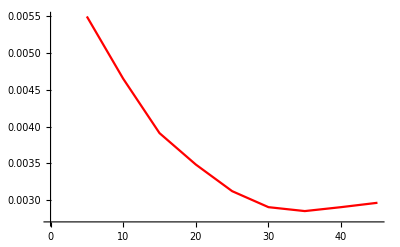

```mathematica
ListLinePlot[misfit[3,0.5,93][[1]],PlotStyle->Red]
```

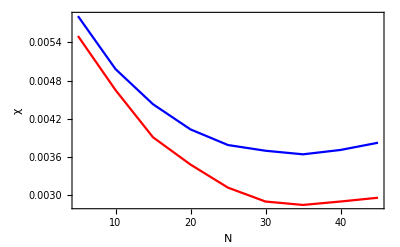

```mathematica
Show[%41,%39,PlotRange->All]
```

```mathematica
N[463/2000]
```

0.2315

```mathematica
102*33
```

3366

```mathematica
FactorInteger[3366]
```

{{2,1},{3,2},{11,1},{17,1}}

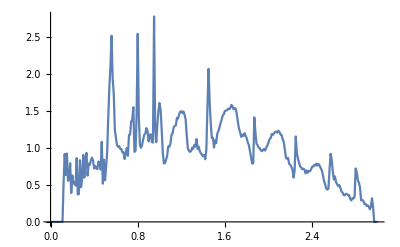

```mathematica
ListPlot[%31,Joined->True]
```